# Domača naloga 2

## Naloga 1

V Mathematici predstavimo daljico v obliki Daljica[AA_, BB_], kjer sta AA in BB točki predstavljeni
s parom koordinat v obliki {x, y}.

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2 = Daljica[{-1, -1}, {3, 1}]
d3 = Daljica[{-1, 2}, {3, 0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

Dolzina[Daljica[AA_, BB_]], ki vrne dolžino daljice

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB -AA]
```

```mathematica
Dolzina[d]
```

2 √5

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

Slika[Daljica[AA_, BB_]], ki vrne grafični objekt Line, kateri predstavlja daljico

```mathematica
Slika[Daljica[AA_,BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

Narisi[d__Daljica], ki za eno ali več podanih daljic le-te izriše

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
```

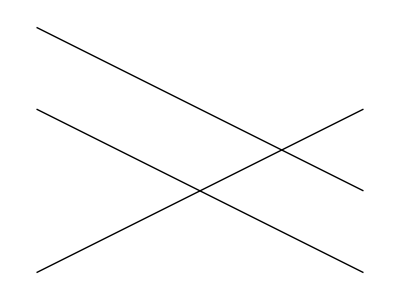

```mathematica
Narisi[d, d2,d3]
```

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

EnacbaNosilke[Daljica[AA_, BB_]], ki vrne enačbo premice nosilke daljice.

```mathematica
ClearAll[x, y]
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2 - x1);
n =n /.First[Solve[y1 == k*x1 + n, n]];
y ==  k*x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

## Naloga 2

Sestavi funkcijo Presek[Daljica[AA_, BB_], Daljica[CC_, DD_]], ki vrne presečišče daljic, če
se sekata, oziroma prazen seznam ({}).

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]
]
```

```mathematica
Presek[d, d2]
```

{1,0}

```mathematica
Presek[d, d3]
```

{}

## Naloga 3

Sklenjen mnogokotnik podamo v obliki seznama z glavo Mnogokotnik.

```mathematica
m1=Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

Prvo funkcijo sem definiral tako, da sem uporabil ukaz Line, kateri se bo skliceval na spremenljivko, katera bom vnesene v funkcijo. Dodamo še njeno prvo točko, da se Mnogokotnik sklene.

```mathematica
Slika[Mnogokotnik[t__]]:=Line[{t,First[m1]}]
```

```mathematica
Slika[m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2},{0,0}}]

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

Funkcija Narisi pokliče predhodno funkcijo, katera ustvari oziroma nariše določene črte, ki so prikazane v ukazu Graphics.

```mathematica
Narisi[m__Mnogokotnik]:=Graphics[Slika[m]]
```

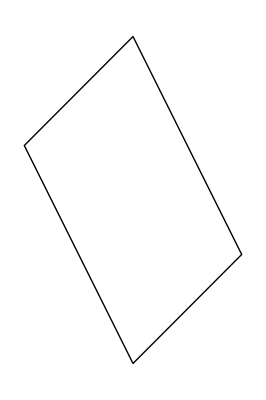

```mathematica
Narisi[m1]
```

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

V tej nalogi funkcijo sklicujem tako, da uporabim račun za točke, ki se nahajajo na koordinatah. To zavijem v ukaz Table, ki ustvari toliko {x,y} točk, kolikor jih je uporabnik vnesel. Table zavijem v ukaz Line, ki s tem ustvari črte med določenimi točkami. Za na konec vse skupaj zavijem v ukaz Graphics, ki poleg tega, da prikaže Mnogokotnik, prikaže tudi njegovo središče, s pomočjo ukazom Point.

```mathematica
PravilniNKotnik[n_,r_]:= Graphics[{Line[{Table[{r* Cos[(2*Pi * i)/n],r*Sin[(2 Pi *i)/n]},{i,0,n}]}],Point[ {0,0}]}]
```

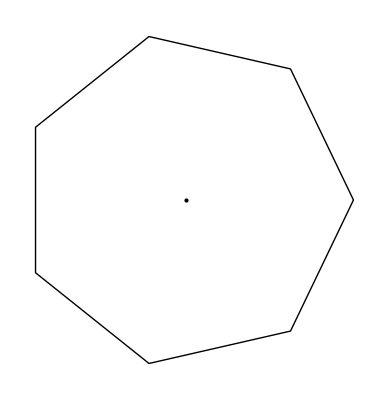

```mathematica
p5=PravilniNKotnik[7,2]
```

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

Potek pri tej nalogi je podoben predhodnji, le da na koncu dodamo ukaz Manipulate, kateri se sklicuje na dodatno neznanko “phi”. Neznanka “phi” omogoča, da rotiramo Mnogokotnik v poljubno smer (min, max).

```mathematica
PravilniNKotnik[n_,r_,phi_]:=Manipulate[Graphics[{Line[{Table[{r* Cos[(2*Pi * i+phi)/n],r*Sin[(2 Pi *i+phi)/n]},{i,0,n}]}],Point[ {0,0}]}]
,{phi,2,20}]
```

```mathematica
PravilniNKotnik[10,3,phi]
```

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

Partition razdeli Listo v pod liste te Liste

```mathematica
Partition[m1,2]
```

Mnogokotnik[Mnogokotnik[{0,0},{1,1}],Mnogokotnik[{0,3},{-1,2}]]

```mathematica
Partition[m1,3,1]
```

Mnogokotnik[Mnogokotnik[{0,0},{1,1},{0,3}],Mnogokotnik[{1,1},{0,3},{-1,2}]]

```mathematica
m1
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

V prvem primeru Partition razdeli točke, skupaj po dva, v pod listo.
V drugem primeru Partition porazdeli točke po 3 in se pri naslednji pod listi zamakne za eno točko naprej.

```mathematica
Dalj=Append[m1,m1[[1]]]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Daljice[Mnogokotnik[t__]]:=Partition[{t},2,1]
```

```mathematica
Map[Daljica,Daljice[Dalj]]
```

{Daljica[{{0,0},{1,1}}],Daljica[{{1,1},{0,3}}],Daljica[{{0,3},{-1,2}}],Daljica[{{-1,2},{0,0}}]}

## Naloga 4

```mathematica
Presek[m_Mnogokotnik,d_Daljica]:=Module[{resitev},
resitev=
]
```

## Naloga 5

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f,sez1,sez2],1]
VsiPari[f,{1,2,3},{a,b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
VsiPari[k,{2,3,4},{7,3,5}]
```

```mathematica
{k[2,7],k[2,3],k[2,5],k[3,7],k[3,3],k[3,5],k[4,7],k[4,3],k[4,5]}
```

```mathematica
VsiPari[f,{{1,2},{3,4}},{{aa,bb},{dd,cc}}]
```

{{{f[1,aa],f[1,bb]},{f[1,dd],f[1,cc]}},{{f[2,aa],f[2,bb]},{f[2,dd],f[2,cc]}},{{f[3,aa],f[3,bb]},{f[3,dd],f[3,cc]}},{{f[4,aa],f[4,bb]},{f[4,dd],f[4,cc]}}}

Outer: skupaj združi sezname ter jih razporedi po vseh možnih načinih (jih lahko tudi vgnezdi).
Flatten: vgnezdene zanke odgnezdi, glede na dano število.

```mathematica
Outer[f,{2,4,3,{5},9}]
```

{f[2],f[4],f[3],{f[5]},f[9]}

```mathematica
Flatten[Outer[f,{2,4,3,{5},9}],1]
```

{f[2],f[4],f[3],f[5],f[9]}

## Naloga 6

Podane so nam točke tristranične piramide A(3,1,1), B(1,3,4), C(-1,-1,1) in D(3,-2,7). Izračunati moram: Ploščino, prostornino, višino in začetno točko “NN” višine, katera je pravokotna na ravnino tristranične piramide.

```mathematica
ClearAll[TriPiramida]
```

```mathematica
TriPiramida=Tetrahedron[{{3,1,1},{1,3,4},{-1,-1,1},{3,-2,7}}];
```

```mathematica
AA=(3,1,1);
BB=(1,3,4);
CC=(-1,-1,1);
DD=(3,-2,7);
```

Poiščemo vektorje, ki si niso koplanarni in se pričnejo v isti točki.

```mathematica
VA=BB-AA
```

{-2,2,3}

```mathematica
VB=CC-AA
```

{-4,-2,0}

```mathematica
VC=DD-AA
```

{0,-3,6}

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

Da dobimo ploščino piramide, rabimo izračunati razdaljo vektorskega produkta.

```mathematica
Produkt[X_,Y_]:=Cross[X,Y]
```

```mathematica
Razdalja[Vek1_,Vek2_]:=(√(Produkt[Vek1,Vek2].Produkt[Vek1,Vek2]))/2
```

```mathematica
Razdalja[VA,VB]
```

9

Dobimo ploščino paralepipeda, zato delimo z 2.

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

Da pridobimo prostornino piramide, vzamemo šestino pridobljene prostornine, za katero smo uporabili enačbo za iskanje prostornine paralepipeda.

```mathematica
ProstorninaPiramide[VA_,VB_,VC_]:=(Produkt[VA,VB].VC)/6
```

```mathematica
ProstorninaPiramide[VA,VB,VC]
```

18

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

Razdaljo višine dobimo tako, da obrnemo enačbo: v=3V/S

```mathematica
Visina[VA_,VB_,VC_]:=Module[{vis,koncna},
vis=(3*ProstorninaPiramide[VA,VB,VC])/Razdalja[VA,VB];
koncna=vis*Produkt[VA,VB]/(Razdalja[VA,VB]*2)
]
```

```mathematica
vektorVisine=Visina[VA,VB,VC]
```

{2,-4,4}

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

Da dobimo še točko “NN”, rabimo uporabiti ničelni vektor.

```mathematica
NN=DD-vektorVisine
```

{1,2,3}

```mathematica
Graphics3D[{{Opacity[0.3],LightBlue,TriPiramida},{PointSize[Large],Red,Point[NN]},{Red,Line[{NN,DD}]}}]
```

-Graphics3D-